```mathematica
slits = 3;
```

```mathematica
e[x_]:= Sum[Exp[ⅈ n x],{n,0,slits-1}]
```

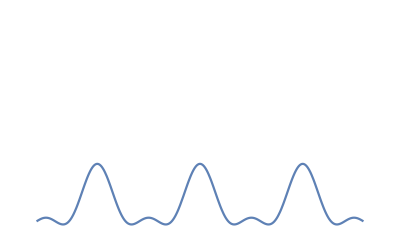

```mathematica
slits = 3;Plot[Abs[e[x]]^2/2,{x,-10,10},PlotRange->{0,15},Axes->False]
```

```mathematica
?Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.

```mathematica
Export["~/three.eps",%185]
```

~/three.eps

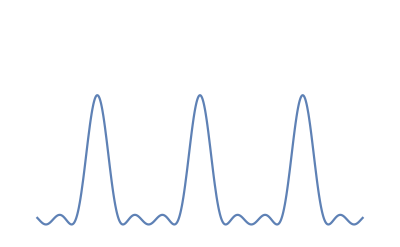

```mathematica
slits = 4;
Plot[Abs[e[x]]^2,{x,-10,10},PlotRange->{0,25},Axes->False]
```

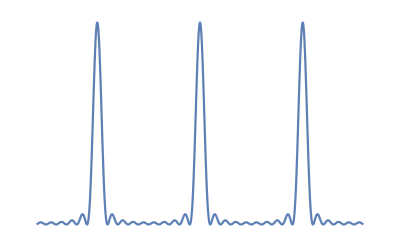

```mathematica
slits = 10;
Plot[Abs[e[x]]^2,{x,-10,10},PlotRange->All,Axes->False]
```

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.